```mathematica
<<Sneg`
```

sneg 2.0.6 Copyright (C) 2002-2023 Rok Zitko

```mathematica
$Assumptions = Δ>0&&t>0
```

Δ>0&&t>0

```mathematica
snegfermionoperators[d]
snegspinlessfermionoperators[a,b]
snegrealconstants[Δ,U,V,t,tso,Vz,Sequence@@Table[μ[n],{n,1,2}],Sequence@@Table[ϕ[n],{n,1,2}],Sequence@@Table[β[n],{n,1,2}]]
```

```mathematica
Conjugate[ϕ[1]]
```

ϕ[1]

```mathematica
pairing[c_[n_]]:=nc[c[0,n,UP],c[0,n,DO]] + nc[c[1,n,DO],c[1,n,UP]]
pairing[Δ_,c_[n_]]:=Δ nc[c[0,n,UP],c[0,n,DO]] + Conjugate[Δ]nc[c[1,n,DO],c[1,n,UP]]
zeeman[c_[n_]]:=-number[c[n],1]+number[c[n],0]
soc[c1_[n1_],c2_[n2_]]:=nc[c1[0,1,0],c2[1,n2,1]] - nc[c1[0,1,1],c2[1,n2,0]]+nc[c2[0,n2,1],c1[1,1,0]] - nc[c2[0,n2,0],c1[1,1,1]]
```

```mathematica
pairing[d[1]]
```

-(d_(1↓)^†·d_(1⇑)^†)+d_(1↓)^·d_(1⇑)^

```mathematica
zeeman[d[1]]
```

d_(1↓)^†·d_(1↓)^-d_(1⇑)^†·d_(1⇑)^

```mathematica
soc[d[1],d[2]]
```

d_(1↓)^†·d_(2⇑)^-d_(1⇑)^†·d_(2↓)^-d_(2↓)^†·d_(1⇑)^+d_(2⇑)^†·d_(1↓)^

```mathematica
hubbard[d[1]]
```

-(d_(1↓)^†·d_(1⇑)^†·d_(1↓)^·d_(1⇑)^)

```mathematica
pairing[Δ Exp[I ϕ[1]],d[1]]
```

-ⅇ^(ⅈ ϕ[1]) Δ d_(1↓)^†·d_(1⇑)^†+ⅇ^(-ⅈ ϕ[1]) Δ d_(1↓)^·d_(1⇑)^

```mathematica
H=Sum[-μ[n] number[d[n]] +pairing[Δ Exp[I ϕ[n]],d[n]]+U hubbard[d[n]] + Vz zeeman[d[n]],{n,1,2}]+t*hop[d[1],d[2]]+tso*soc[d[1],d[2]]+V nc[number[d[1]],number[d[2]]]//Expand
```

-ⅇ^(ⅈ ϕ[1]) Δ d_(1↓)^†·d_(1⇑)^†+Vz d_(1↓)^†·d_(1↓)^+t d_(1↓)^†·d_(2↓)^+tso d_(1↓)^†·d_(2⇑)^-Vz d_(1⇑)^†·d_(1⇑)^-tso d_(1⇑)^†·d_(2↓)^+t d_(1⇑)^†·d_(2⇑)^-ⅇ^(ⅈ ϕ[2]) Δ d_(2↓)^†·d_(2⇑)^†+t d_(2↓)^†·d_(1↓)^-tso d_(2↓)^†·d_(1⇑)^+Vz d_(2↓)^†·d_(2↓)^+tso d_(2⇑)^†·d_(1↓)^+t d_(2⇑)^†·d_(1⇑)^-Vz d_(2⇑)^†·d_(2⇑)^+ⅇ^(-ⅈ ϕ[1]) Δ d_(1↓)^·d_(1⇑)^+ⅇ^(-ⅈ ϕ[2]) Δ d_(2↓)^·d_(2⇑)^-U d_(1↓)^†·d_(1⇑)^†·d_(1↓)^·d_(1⇑)^-V d_(1↓)^†·d_(2↓)^†·d_(1↓)^·d_(2↓)^-V d_(1↓)^†·d_(2⇑)^†·d_(1↓)^·d_(2⇑)^-V d_(1⇑)^†·d_(2↓)^†·d_(1⇑)^·d_(2↓)^-V d_(1⇑)^†·d_(2⇑)^†·d_(1⇑)^·d_(2⇑)^-U d_(2↓)^†·d_(2⇑)^†·d_(2↓)^·d_(2⇑)^-d_(1↓)^†·d_(1↓)^ μ[1]-d_(1⇑)^†·d_(1⇑)^ μ[1]-d_(2↓)^†·d_(2↓)^ μ[2]-d_(2⇑)^†·d_(2⇑)^ μ[2]

```mathematica
abdefs = {a[1,n]==Exp[I ϕ[n]/2]/Sqrt[2β[n]](Sqrt[β[n]+μ[n]]d[0,n,DO]+Exp[-I ϕ[n]]Sqrt[β[n]-μ[n]]d[1,n,UP]),b[1,n]==Exp[I ϕ[n]/2]/Sqrt[2β[n]](Sqrt[β[n]+μ[n]]d[0,n,UP]-Exp[-I ϕ[n]]Sqrt[β[n]-μ[n]]d[1,n,DO]),
a[0,n]==Exp[-I ϕ[n]/2]/Sqrt[2β[n]](Sqrt[β[n]+μ[n]]d[1,n,DO]+Exp[I ϕ[n]]Sqrt[β[n]-μ[n]]d[0,n,UP]),b[0,n]==Exp[-I ϕ[n]/2]/Sqrt[2β[n]](Sqrt[β[n]+μ[n]]d[1,n,UP]-Exp[I ϕ[n]]Sqrt[β[n]-μ[n]]d[0,n,DO])}(*/.{μ[n_]:>-μ[n]};*)
```

{a_n^==(ⅇ^(1/2 ⅈ ϕ[n]) (ⅇ^(-ⅈ ϕ[n]) d_(n⇑)^ √(β[n]-μ[n])+d_(n↓)^† √(β[n]+μ[n])))/(√2 √β[n]),b_n^==(ⅇ^(1/2 ⅈ ϕ[n]) (-ⅇ^(-ⅈ ϕ[n]) d_(n↓)^ √(β[n]-μ[n])+d_(n⇑)^† √(β[n]+μ[n])))/(√2 √β[n]),a_n^†==(ⅇ^(-1/2 ⅈ ϕ[n]) (ⅇ^(ⅈ ϕ[n]) d_(n⇑)^† √(β[n]-μ[n])+d_(n↓)^ √(β[n]+μ[n])))/(√2 √β[n]),b_n^†==(ⅇ^(-1/2 ⅈ ϕ[n]) (-ⅇ^(ⅈ ϕ[n]) d_(n↓)^† √(β[n]-μ[n])+d_(n⇑)^ √(β[n]+μ[n])))/(√2 √β[n])}

```mathematica
abdefs
```

{a_n^==(ⅇ^(1/2 ⅈ ϕ[n]) (d_(n↓)^† √(β[n]-μ[n])+ⅇ^(-ⅈ ϕ[n]) d_(n⇑)^ √(β[n]+μ[n])))/(√2 √β[n]),b_n^==(ⅇ^(1/2 ⅈ ϕ[n]) (d_(n⇑)^† √(β[n]-μ[n])-ⅇ^(-ⅈ ϕ[n]) d_(n↓)^ √(β[n]+μ[n])))/(√2 √β[n]),a_n^†==(ⅇ^(-1/2 ⅈ ϕ[n]) (d_(n↓)^ √(β[n]-μ[n])+ⅇ^(ⅈ ϕ[n]) d_(n⇑)^† √(β[n]+μ[n])))/(√2 √β[n]),b_n^†==(ⅇ^(-1/2 ⅈ ϕ[n]) (d_(n⇑)^ √(β[n]-μ[n])-ⅇ^(ⅈ ϕ[n]) d_(n↓)^† √(β[n]+μ[n])))/(√2 √β[n])}

```mathematica
Assuming[μ[n]∈Reals,abdefs/.βsub/.Δ->0//FullSimplify]
```

{ⅇ^(ⅈ ϕ[n]) d_(n↓)^† √(2-2 Sign[μ[n]])+√2 d_(n⇑)^ √(1+Sign[μ[n]])==2 ⅇ^(1/2 ⅈ ϕ[n]) a_n^,ⅇ^(ⅈ ϕ[n]) d_(n⇑)^† √(2-2 Sign[μ[n]])==2 ⅇ^(1/2 ⅈ ϕ[n]) b_n^+√2 d_(n↓)^ √(1+Sign[μ[n]]),d_(n↓)^ √(2-2 Sign[μ[n]])+√2 ⅇ^(ⅈ ϕ[n]) d_(n⇑)^† √(1+Sign[μ[n]])==2 ⅇ^(1/2 ⅈ ϕ[n]) a_n^†,2 ⅇ^(1/2 ⅈ ϕ[n]) b_n^†+√2 ⅇ^(ⅈ ϕ[n]) d_(n↓)^† √(1+Sign[μ[n]])==d_(n⇑)^ √(2-2 Sign[μ[n]])}

```mathematica
dfromab = Solve[abdefs, {d[0,n,DO],d[1,n,DO],d[0,n,UP],d[1,n,UP]}]//FullSimplify
```

{{d_(n↓)^†→(ⅇ^(-1/2 ⅈ ϕ[n]) (-b_n^† √(β[n]-μ[n])+a_n^ √(β[n]+μ[n])))/(√2 √β[n]),d_(n↓)^→(ⅇ^(1/2 ⅈ ϕ[n]) (-b_n^ √(β[n]-μ[n])+a_n^† √(β[n]+μ[n])))/(√2 √β[n]),d_(n⇑)^†→(ⅇ^(-1/2 ⅈ ϕ[n]) (a_n^† √(β[n]-μ[n])+b_n^ √(β[n]+μ[n])))/(√2 √β[n]),d_(n⇑)^→(ⅇ^(1/2 ⅈ ϕ[n]) (a_n^ √(β[n]-μ[n])+b_n^† √(β[n]+μ[n])))/(√2 √β[n])}}

```mathematica
dsub = dfromab[[1]]/.Rule[a_,b_]:>RuleDelayed[a,b]/.d[x_,n,c_]:>d[x,n_,c]//FullSimplify;
```

```mathematica
Hab = H/.dsub//Simplify;
```

```mathematica
(*vacuumsubs = {nc[b[0,_],b[1,_]]->0,nc[b[x__],b[y__]]:>0,nc[a[x__],b[y__]]:>0,nc[b[a__],a[b__]]:>0,
nc[b[a__],b[b__],c__]:>0,
nc[b[a__],a[b__],c__]:>0,
nc[a__,b[b__],c__]:>0
}*)
```

```mathematica
Hab
```

-1/(2 β[1] β[2])(-2 U β[1] β[2]-2 V β[1] β[2]+U b_1^†·b_1^ β[1] β[2]-2 Vz b_1^†·b_1^ β[1] β[2]+U b_2^†·b_2^ β[1] β[2]-2 Vz b_2^†·b_2^ β[1] β[2]+2 U a_1^†·b_1^†·a_1^·b_1^ β[1] β[2]+2 U a_2^†·b_2^†·a_2^·b_2^ β[1] β[2]-U β[2] μ[1]-2 V β[2] μ[1]-2 Δ a_1^†·b_1^† β[2] μ[1]+2 Δ a_1^·b_1^ β[2] μ[1]+U b_1^†·b_1^ β[2] μ[1]+2 V b_1^†·b_1^ β[2] μ[1]+2 β[1] β[2] μ[1]+2 β[2] μ[1]^2-2 b_1^†·b_1^ β[2] μ[1]^2+2 Δ β[2] √(β[1]-μ[1]) √(β[1]+μ[1])-U a_1^†·b_1^† β[2] √(β[1]-μ[1]) √(β[1]+μ[1])-2 V a_1^†·b_1^† β[2] √(β[1]-μ[1]) √(β[1]+μ[1])+U a_1^·b_1^ β[2] √(β[1]-μ[1]) √(β[1]+μ[1])+2 V a_1^·b_1^ β[2] √(β[1]-μ[1]) √(β[1]+μ[1])-2 Δ b_1^†·b_1^ β[2] √(β[1]-μ[1]) √(β[1]+μ[1])+2 a_1^†·b_1^† β[2] √(β[1]-μ[1]) μ[1] √(β[1]+μ[1])-2 a_1^·b_1^ β[2] √(β[1]-μ[1]) μ[1] √(β[1]+μ[1])-ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) t a_1^†·a_2^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]-μ[2])-ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) tso a_1^†·b_2^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]-μ[2])-ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) t a_2^†·a_1^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]-μ[2])+ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) tso a_2^†·b_1^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]-μ[2])+ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) tso b_1^†·a_2^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]-μ[2])-ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) t b_1^†·b_2^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]-μ[2])-ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) tso b_2^†·a_1^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]-μ[2])-ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) t b_2^†·b_1^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]-μ[2])+ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) tso a_1^†·a_2^† √β[1] √β[2] √(β[1]+μ[1]) √(β[2]-μ[2])-ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) t a_1^†·b_2^† √β[1] √β[2] √(β[1]+μ[1]) √(β[2]-μ[2])-ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) t a_2^†·b_1^† √β[1] √β[2] √(β[1]+μ[1]) √(β[2]-μ[2])-ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) tso a_1^·a_2^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]-μ[2])+ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) t a_1^·b_2^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]-μ[2])+ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) t a_2^·b_1^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]-μ[2])+ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) tso b_1^†·b_2^† √β[1] √β[2] √(β[1]+μ[1]) √(β[2]-μ[2])-ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) tso b_1^·b_2^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]-μ[2])-U β[1] μ[2]-2 V β[1] μ[2]-2 Δ a_2^†·b_2^† β[1] μ[2]+2 Δ a_2^·b_2^ β[1] μ[2]+U b_2^†·b_2^ β[1] μ[2]+2 V b_2^†·b_2^ β[1] μ[2]+2 β[1] β[2] μ[2]-2 V μ[1] μ[2]+2 V b_1^†·b_1^ μ[1] μ[2]+2 V b_2^†·b_2^ μ[1] μ[2]+2 V a_1^†·a_2^†·a_1^·a_2^ μ[1] μ[2]+2 V a_1^†·b_2^†·a_1^·b_2^ μ[1] μ[2]+2 V a_2^†·b_1^†·a_2^·b_1^ μ[1] μ[2]+2 V b_1^†·b_2^†·b_1^·b_2^ μ[1] μ[2]-2 V a_1^†·b_1^† √(β[1]-μ[1]) √(β[1]+μ[1]) μ[2]+2 V a_1^·b_1^ √(β[1]-μ[1]) √(β[1]+μ[1]) μ[2]-2 V a_1^†·a_2^†·b_1^†·a_2^ √(β[1]-μ[1]) √(β[1]+μ[1]) μ[2]+2 V a_1^†·b_1^†·b_2^†·b_2^ √(β[1]-μ[1]) √(β[1]+μ[1]) μ[2]+2 V a_2^†·a_1^·a_2^·b_1^ √(β[1]-μ[1]) √(β[1]+μ[1]) μ[2]-2 V b_2^†·a_1^·b_1^·b_2^ √(β[1]-μ[1]) √(β[1]+μ[1]) μ[2]+2 β[1] μ[2]^2-2 b_2^†·b_2^ β[1] μ[2]^2+ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) tso a_1^†·a_2^† √β[1] √β[2] √(β[1]-μ[1]) √(β[2]+μ[2])-ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) t a_1^†·b_2^† √β[1] √β[2] √(β[1]-μ[1]) √(β[2]+μ[2])-ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) t a_2^†·b_1^† √β[1] √β[2] √(β[1]-μ[1]) √(β[2]+μ[2])-ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) tso a_1^·a_2^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]+μ[2])+ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) t a_1^·b_2^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]+μ[2])+ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) t a_2^·b_1^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]+μ[2])+ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) tso b_1^†·b_2^† √β[1] √β[2] √(β[1]-μ[1]) √(β[2]+μ[2])-ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) tso b_1^·b_2^ √β[1] √β[2] √(β[1]-μ[1]) √(β[2]+μ[2])+ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) t a_1^†·a_2^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]+μ[2])+ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) tso a_1^†·b_2^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]+μ[2])+ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) t a_2^†·a_1^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]+μ[2])-ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) tso a_2^†·b_1^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]+μ[2])-ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) tso b_1^†·a_2^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]+μ[2])+ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) t b_1^†·b_2^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]+μ[2])+ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) tso b_2^†·a_1^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]+μ[2])+ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) t b_2^†·b_1^ √β[1] √β[2] √(β[1]+μ[1]) √(β[2]+μ[2])+2 Δ β[1] √(β[2]-μ[2]) √(β[2]+μ[2])-U a_2^†·b_2^† β[1] √(β[2]-μ[2]) √(β[2]+μ[2])-2 V a_2^†·b_2^† β[1] √(β[2]-μ[2]) √(β[2]+μ[2])+U a_2^·b_2^ β[1] √(β[2]-μ[2]) √(β[2]+μ[2])+2 V a_2^·b_2^ β[1] √(β[2]-μ[2]) √(β[2]+μ[2])-2 Δ b_2^†·b_2^ β[1] √(β[2]-μ[2]) √(β[2]+μ[2])-2 V a_2^†·b_2^† μ[1] √(β[2]-μ[2]) √(β[2]+μ[2])+2 V a_2^·b_2^ μ[1] √(β[2]-μ[2]) √(β[2]+μ[2])+2 V a_1^†·a_2^†·b_2^†·a_1^ μ[1] √(β[2]-μ[2]) √(β[2]+μ[2])-2 V a_1^†·a_1^·a_2^·b_2^ μ[1] √(β[2]-μ[2]) √(β[2]+μ[2])-2 V a_2^†·b_1^†·b_2^†·b_1^ μ[1] √(β[2]-μ[2]) √(β[2]+μ[2])+2 V b_1^†·a_2^·b_1^·b_2^ μ[1] √(β[2]-μ[2]) √(β[2]+μ[2])+2 V a_1^†·a_2^†·b_1^†·b_2^† √(β[1]-μ[1]) √(β[1]+μ[1]) √(β[2]-μ[2]) √(β[2]+μ[2])+2 V a_1^†·b_1^†·a_2^·b_2^ √(β[1]-μ[1]) √(β[1]+μ[1]) √(β[2]-μ[2]) √(β[2]+μ[2])+2 V a_2^†·b_2^†·a_1^·b_1^ √(β[1]-μ[1]) √(β[1]+μ[1]) √(β[2]-μ[2]) √(β[2]+μ[2])+2 V a_1^·a_2^·b_1^·b_2^ √(β[1]-μ[1]) √(β[1]+μ[1]) √(β[2]-μ[2]) √(β[2]+μ[2])+2 a_2^†·b_2^† β[1] √(β[2]-μ[2]) μ[2] √(β[2]+μ[2])-2 a_2^·b_2^ β[1] √(β[2]-μ[2]) μ[2] √(β[2]+μ[2])+a_1^†·a_1^ (2 Vz β[1] β[2]+U β[2] (β[1]+μ[1])-2 β[2] (μ[1]^2+Δ √(β[1]-μ[1]) √(β[1]+μ[1]))+2 V μ[1] (β[2]+μ[2]))+a_2^†·a_2^ (2 Vz β[1] β[2]+2 V (β[1]+μ[1]) μ[2]+U β[1] (β[2]+μ[2])-2 β[1] (μ[2]^2+Δ √(β[2]-μ[2]) √(β[2]+μ[2]))))

```mathematica
vacuumsubs = {nc[a___,b[b__],c___]:>0}
```

{a___·b[b__]·c___:>0}

```mathematica
βsub = {β[j_]:>Sqrt[μ[j]^2+Δ^2]}
```

{β[j_]:>√(μ[j]^2+Δ^2)}

```mathematica
nonintμsub = {μ[n_]:>(-1)^(1+n)Sqrt[Vz^2-Δ^2]}
```

{μ[n_]:>(-1)^(1+n) √(Vz^2-Δ^2)}

```mathematica
nonintHab = Assuming[Vz>Δ,Hab/.{U->0,V->0}/.βsub/.nonintμsub//Simplify];
```

```mathematica
Ha = Hab/.vacuumsubs//Simplify//Expand
```

U+V-1/2 U a_1^†·a_1^-Vz a_1^†·a_1^-1/2 U a_2^†·a_2^-Vz a_2^†·a_2^-μ[1]+(U μ[1])/(2 β[1])+(V μ[1])/β[1]-(U a_1^†·a_1^ μ[1])/(2 β[1])-(V a_1^†·a_1^ μ[1])/β[1]-μ[1]^2/β[1]+(a_1^†·a_1^ μ[1]^2)/β[1]-(Δ √(β[1]-μ[1]) √(β[1]+μ[1]))/β[1]+(Δ a_1^†·a_1^ √(β[1]-μ[1]) √(β[1]+μ[1]))/β[1]+(ⅇ^(-1/2 ⅈ ϕ[1]+1/2 ⅈ ϕ[2]) t a_1^†·a_2^ √(β[1]-μ[1]) √(β[2]-μ[2]))/(2 √β[1] √β[2])+(ⅇ^(1/2 ⅈ ϕ[1]-1/2 ⅈ ϕ[2]) t a_2^†·a_1^ √(β[1]-μ[1]) √(β[2]-μ[2]))/(2 √β[1] √β[2])-(ⅇ^(1/2 ⅈ ϕ[1]-1/2 ⅈ ϕ[2]) tso a_1^†·a_2^† √(β[1]+μ[1]) √(β[2]-μ[2]))/(2 √β[1] √β[2])+(ⅇ^(-1/2 ⅈ ϕ[1]+1/2 ⅈ ϕ[2]) tso a_1^·a_2^ √(β[1]+μ[1]) √(β[2]-μ[2]))/(2 √β[1] √β[2])-μ[2]+(U μ[2])/(2 β[2])+(V μ[2])/β[2]-(U a_2^†·a_2^ μ[2])/(2 β[2])-(V a_2^†·a_2^ μ[2])/β[2]+(V μ[1] μ[2])/(β[1] β[2])-(V a_1^†·a_1^ μ[1] μ[2])/(β[1] β[2])-(V a_2^†·a_2^ μ[1] μ[2])/(β[1] β[2])-(V a_1^†·a_2^†·a_1^·a_2^ μ[1] μ[2])/(β[1] β[2])-μ[2]^2/β[2]+(a_2^†·a_2^ μ[2]^2)/β[2]-(ⅇ^(-1/2 ⅈ ϕ[1]+1/2 ⅈ ϕ[2]) tso a_1^†·a_2^† √(β[1]-μ[1]) √(β[2]+μ[2]))/(2 √β[1] √β[2])+(ⅇ^(1/2 ⅈ ϕ[1]-1/2 ⅈ ϕ[2]) tso a_1^·a_2^ √(β[1]-μ[1]) √(β[2]+μ[2]))/(2 √β[1] √β[2])-(ⅇ^(1/2 ⅈ ϕ[1]-1/2 ⅈ ϕ[2]) t a_1^†·a_2^ √(β[1]+μ[1]) √(β[2]+μ[2]))/(2 √β[1] √β[2])-(ⅇ^(-1/2 ⅈ ϕ[1]+1/2 ⅈ ϕ[2]) t a_2^†·a_1^ √(β[1]+μ[1]) √(β[2]+μ[2]))/(2 √β[1] √β[2])-(Δ √(β[2]-μ[2]) √(β[2]+μ[2]))/β[2]+(Δ a_2^†·a_2^ √(β[2]-μ[2]) √(β[2]+μ[2]))/β[2]

```mathematica
nonintHa = Assuming[Vz>Δ,Ha/.{V->0,U->0}/.βsub/.nonintμsub//Simplify]
```

1/(2 Abs[Vz])ⅇ^(-1/2 ⅈ (ϕ[1]+ϕ[2])) (-4 ⅇ^(1/2 ⅈ (ϕ[1]+ϕ[2])) Vz^2+4 ⅇ^(1/2 ⅈ (ϕ[1]+ϕ[2])) Δ^2-tso ((ⅇ^(ⅈ ϕ[1])-ⅇ^(ⅈ ϕ[2])) √(Vz^2-Δ^2)+(ⅇ^(ⅈ ϕ[1])+ⅇ^(ⅈ ϕ[2])) Abs[Vz]) a_1^†·a_2^†+2 ⅇ^(1/2 ⅈ (ϕ[1]+ϕ[2])) Vz^2 a_1^†·a_1^-2 ⅇ^(1/2 ⅈ (ϕ[1]+ϕ[2])) Δ^2 a_1^†·a_1^-2 ⅇ^(1/2 ⅈ (ϕ[1]+ϕ[2])) Vz Abs[Vz] a_1^†·a_1^+2 ⅇ^(1/2 ⅈ (ϕ[1]+ϕ[2])) Vz^2 a_2^†·a_2^-2 ⅇ^(1/2 ⅈ (ϕ[1]+ϕ[2])) Δ^2 a_2^†·a_2^-2 ⅇ^(1/2 ⅈ (ϕ[1]+ϕ[2])) Vz Abs[Vz] a_2^†·a_2^+Abs[Δ] (-4 ⅇ^(1/2 ⅈ (ϕ[1]+ϕ[2])) Δ+2 ⅇ^(1/2 ⅈ (ϕ[1]+ϕ[2])) Δ a_1^†·a_1^-(ⅇ^(ⅈ ϕ[1])-ⅇ^(ⅈ ϕ[2])) t a_1^†·a_2^+ⅇ^(ⅈ ϕ[1]) t a_2^†·a_1^-ⅇ^(ⅈ ϕ[2]) t a_2^†·a_1^+2 ⅇ^(1/2 ⅈ (ϕ[1]+ϕ[2])) Δ a_2^†·a_2^)-ⅇ^(ⅈ ϕ[1]) tso √(Vz^2-Δ^2) a_1^·a_2^+ⅇ^(ⅈ ϕ[2]) tso √(Vz^2-Δ^2) a_1^·a_2^+ⅇ^(ⅈ ϕ[1]) tso Abs[Vz] a_1^·a_2^+ⅇ^(ⅈ ϕ[2]) tso Abs[Vz] a_1^·a_2^)

```mathematica
Coefficient[Hab,nc[a[0,2],a[1,2]]]
```

-(2 Vz β[1] β[2]+2 V (β[1]+μ[1]) μ[2]+U β[1] (β[2]+μ[2])-2 β[1] (μ[2]^2+Δ √(β[2]-μ[2]) √(β[2]+μ[2])))/(2 β[1] β[2])

```mathematica
Assuming[Vz>Δ>0,Coefficient[Hab,nc[a[0,2],a[1,2]]]/.{V->0,U->0}/.βsub/.nonintμsub//FullSimplify]
```

0

```mathematica
Assuming[Vz>Δ>0,Coefficient[Hab,nc[b[0,2],b[1,2]]]/.{V->0,U->0}/.βsub/.nonintμsub//FullSimplify]
```

2 Vz

```mathematica
Coefficient[Ha,nc[a[0,2],a[1,2]]]//FullSimplify
```

-Vz-1/(2 β[1] β[2])(2 V (β[1]+μ[1]) μ[2]+U β[1] (β[2]+μ[2])-2 β[1] (μ[2]^2+Δ √(β[2]-μ[2]) √(β[2]+μ[2])))

```mathematica
Coefficient[Hab,nc[a[0,1],a[1,2]]]
```

-(ⅇ^(1/2 ⅈ (ϕ[1]-ϕ[2])) t √β[1] √β[2] √(β[1]-μ[1]) √(β[2]-μ[2])-ⅇ^(-1/2 ⅈ (ϕ[1]-ϕ[2])) t √β[1] √β[2] √(β[1]+μ[1]) √(β[2]+μ[2]))/(2 β[1] β[2])

```mathematica
tK = Coefficient[Ha,nc[a[1,1],a[1,2]]]//FullSimplify//ExpToTrig//Simplify//Expand//Simplify
```

1/(2 √β[1] √β[2])tso (-ⅈ Sin[1/2 (ϕ[1]-ϕ[2])] (√(β[1]+μ[1]) √(β[2]-μ[2])-√(β[1]-μ[1]) √(β[2]+μ[2]))+Cos[1/2 (ϕ[1]-ϕ[2])] (√(β[1]+μ[1]) √(β[2]-μ[2])+√(β[1]-μ[1]) √(β[2]+μ[2])))

```mathematica
ΔK = Coefficient[Ha,nc[a[0,1],a[1,2]]]//FullSimplify//ExpToTrig//Simplify//Expand//Simplify
```

(t (Cos[1/2 (ϕ[1]-ϕ[2])] (√(β[1]-μ[1]) √(β[2]-μ[2])-√(β[1]+μ[1]) √(β[2]+μ[2]))-ⅈ Sin[1/2 (ϕ[1]-ϕ[2])] (√(β[1]-μ[1]) √(β[2]-μ[2])+√(β[1]+μ[1]) √(β[2]+μ[2]))))/(2 √β[1] √β[2])

```mathematica
VK = Coefficient[Ha,nc[a[0,1],a[1,1],a[0,2],a[1,2]]]//FullSimplify//ExpToTrig//Simplify//Expand//Simplify
```

(V μ[1] μ[2])/(β[1] β[2])

```mathematica
Assuming[β[1]>μ[1]>0&&β[2]>μ[2]>0&&β[1]>0&&β[2]>0,ΔK*Conjugate[ΔK]//Simplify//FullSimplify]
```

(tso^2 (β[1] β[2]-μ[1] μ[2]+Cos[ϕ[1]-ϕ[2]] √((β[1]^2-μ[1]^2) (β[2]^2-μ[2]^2))))/(2 β[1] β[2])

```mathematica
Assuming[β[1]>μ[1]>0&&β[2]>μ[2]>0&&β[1]>0&&β[2]>0,tK*Conjugate[tK]//Simplify//FullSimplify]
```

(t^2 (β[1] β[2]+μ[1] μ[2]-Cos[ϕ[1]-ϕ[2]] √((β[1]^2-μ[1]^2) (β[2]^2-μ[2]^2))))/(2 β[1] β[2])

```mathematica
sweetspoteq = Sqrt[(tso^2 (β[1] β[2]-μ[1] μ[2]+Cos[ϕ[1]-ϕ[2]] √((β[1]^2-μ[1]^2) (β[2]^2-μ[2]^2))))/(2 β[1] β[2])]+VK/2==Sqrt[(t^2 (β[1] β[2]+μ[1] μ[2]-Cos[ϕ[1]-ϕ[2]] √((β[1]^2-μ[1]^2) (β[2]^2-μ[2]^2))))/(2 β[1] β[2])]
```

-(V μ[1] μ[2])/(2 β[1] β[2])+(√((tso^2 (β[1] β[2]-μ[1] μ[2]+Cos[ϕ[1]-ϕ[2]] √((β[1]^2-μ[1]^2) (β[2]^2-μ[2]^2))))/(β[1] β[2])))/(√2)==(√((t^2 (β[1] β[2]+μ[1] μ[2]-Cos[ϕ[1]-ϕ[2]] √((β[1]^2-μ[1]^2) (β[2]^2-μ[2]^2))))/(β[1] β[2])))/(√2)

```mathematica
ϕsols = Solve[sweetspoteq/.ϕ[2]->ϕ[1]+δϕ, δϕ];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
(ϕsols/.{aV->0}/.βsub/.{aΔ->1,tso->t*tratio})[[2]]//Simplify
```

{δϕ→ArcCos[(t^2 (-1+tratio^2) V^2 √(Δ^4) μ[1]^2 μ[2]^2-2 √(Δ^2+μ[1]^2) √(Δ^2+μ[2]^2) √(t^4 tratio^2 V^2 Δ^4 μ[1]^2 μ[2]^2 (4 t^2 (1+tratio^2)-(V^2 μ[1]^2 μ[2]^2)/((Δ^2+μ[1]^2) (Δ^2+μ[2]^2))))-2 t^4 (1+tratio^2) √(Δ^4) ((-1+tratio^2) Δ^4+(-1+tratio^2) Δ^2 (μ[1]^2+μ[2]^2)+μ[1] μ[2] ((-1+tratio^2) μ[1] μ[2]-(1+tratio^2) √(Δ^2+μ[1]^2) √(Δ^2+μ[2]^2))))/(2 t^4 (1+tratio^2)^2 Δ^4 √(Δ^2+μ[1]^2) √(Δ^2+μ[2]^2))]}

```mathematica
%94/.{t->.5,tratio->.2,Δ->1,μ[1]->-1,μ[2]->1,V->1}
```

{δϕ→2.34456}

```mathematica
μmbexpression={-√((Vz+U/2)^2-Δ^2)+U/2,√((Vz+U/2)^2-Δ^2)+U/2}
```

{U/2-√((U/2+Vz)^2-Δ^2),U/2+√((U/2+Vz)^2-Δ^2)}

```mathematica
Series[,{U,0,1}]//Simplify
```

{-√(Vz^2-Δ^2)+(1/2-Vz/(2 √(Vz^2-Δ^2))) U+O[U]^2,√(Vz^2-Δ^2)+1/2 (1+Vz/(√(Vz^2-Δ^2))) U+O[U]^2}

```mathematica
Table[Solve[μ==tratio^-1*Δ,Vz],{μ,μmbexpression}]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{{Vz→1/2 (-U-√(U^2+(4 Δ (-tratio U+Δ+tratio^2 Δ))/tratio^2))},{Vz→1/2 (-U+√(U^2+(4 Δ (-tratio U+Δ+tratio^2 Δ))/tratio^2))}},{{Vz→1/2 (-U-√(U^2+(4 Δ (-tratio U+Δ+tratio^2 Δ))/tratio^2))},{Vz→1/2 (-U+√(U^2+(4 Δ (-tratio U+Δ+tratio^2 Δ))/tratio^2))}}}

```mathematica
Assuming[tratio>0&&Δ>0&&U>0,Series[Vz/.%35,{U,0,1}]//FullSimplify]
```

{{-(√(1+tratio^2) Δ)/tratio+1/2 (-1+1/(√(1+tratio^2))) U+O[U]^2,(√(1+tratio^2) Δ)/tratio+(-1/2-1/(2 √(1+tratio^2))) U+O[U]^2},{-(√(1+tratio^2) Δ)/tratio+1/2 (-1+1/(√(1+tratio^2))) U+O[U]^2,(√(1+tratio^2) Δ)/tratio+(-1/2-1/(2 √(1+tratio^2))) U+O[U]^2}}

```mathematica
Assuming[tratio>0&&Δ==1&&U>0,Solve[μmbexpression[[1]]^2+Δ^2==Sqrt[1+tratio^-2]^2,Vz]//FullSimplify]
```

```mathematica
{{Vz->ConditionalExpression[-(tratio U+√(4+4 tratio U+tratio^2 (4+U^2)))/(2 tratio), 2 tratio≠√5]},{Vz->ConditionalExpression[(-tratio U+√(4+4 tratio U+tratio^2 (4+U^2)))/(2 tratio), 2 tratio≠√5]},{Vz->ConditionalExpression[-(tratio U+√(4-4 tratio U+tratio^2 (4+U^2)))/(2 tratio), tratio Sneg`U≤3+√(5-4 tratio^2)&&((tratio>1&&2 tratio<√5&&√(5-4 tratio^2)+tratio Sneg`U≥3)||(tratio Sneg`U>2&&tratio≤1))]},{Vz->ConditionalExpression[(-tratio U+√(4-4 tratio U+tratio^2 (4+U^2)))/(2 tratio), ]},{Vz->ConditionalExpression[-(tratio U+√(4-4 tratio U+tratio^2 (4+U^2)))/(2 tratio), ]},{Vz->ConditionalExpression[(-tratio U+√(4-4 tratio U+tratio^2 (4+U^2)))/(2 tratio), ]}}
```

```mathematica
Assuming[tratio>0&&Δ==1&&U>0,Series[Vz/.%77,{U,0,2}]//FullSimplify]
```

{-(√(1+tratio^2))/tratio+1/2 (-1+1/(√(1+tratio^2))) U-(tratio^3 U^2)/(8 (1+tratio^2)^(3/2))+O[U]^3,(√(1+tratio^2))/tratio+1/2 (-1-1/(√(1+tratio^2))) U+(tratio^3 U^2)/(8 (1+tratio^2)^(3/2))+O[U]^3,-(√(1+tratio^2))/tratio+1/2 (-1-1/(√(1+tratio^2))) U-(tratio^3 U^2)/(8 (1+tratio^2)^(3/2))+O[U]^3,(√(1+tratio^2))/tratio+1/2 (-1+1/(√(1+tratio^2))) U+(tratio^3 U^2)/(8 (1+tratio^2)^(3/2))+O[U]^3}

```mathematica
Solve[μmbexpression[[1]]==tratio^-1*Δ,U]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{U→(Δ^2+tratio^2 (-Vz^2+Δ^2))/(tratio (tratio Vz+Δ))}}

```mathematica
Solve[μmbexpression[[2]]==tratio^-1*Δ,U]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{U→(Δ^2+tratio^2 (-Vz^2+Δ^2))/(tratio (tratio Vz+Δ))}}

```mathematica
%56/.Vz->h Δ/.Δ->1//Simplify
```

{{U→(1+tratio^2-h^2 tratio^2)/(tratio+h tratio^2)}}

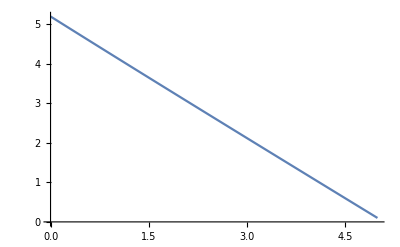

```mathematica
Plot[U/.%57[[1]]/.{tratio->.2,Δ->1},{Vz,0,5}]
```

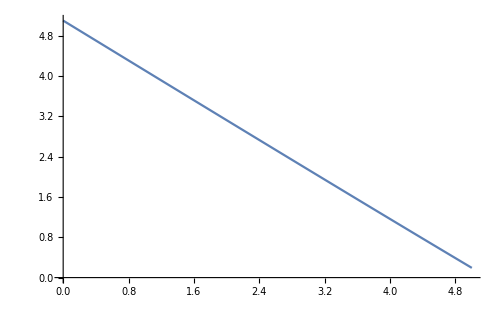

```mathematica
Plot[Vz/.%46[[2]]/.{Δ->1,tratio->.2}//Evaluate,{U,0,5}]
```

```mathematica
μmbsub={μ[1]->-√((Vz+U/2)^2-Δ^2)+U/2,μ[2]->√((Vz+U/2)^2-Δ^2)+U/2}
```

{μ[1]→U/2-√((U/2+Vz)^2-Δ^2),μ[2]→U/2+√((U/2+Vz)^2-Δ^2)}

```mathematica
μmbexpression/.{U->0,Vz->1.5Δ}
```

{-1.11803 √(Δ^2),1.11803 √(Δ^2)}

```mathematica
%68/.{tratio->.2}/.μmbsub/.{Δ->1,Vz->1.5,U->2}//Simplify
```

{{δϕ→-0.36001},{δϕ→0.36001},{δϕ→-0.36001},{δϕ→0.36001}}

```mathematica
Assuming[Vz>Δ,tK/.{U->0,V->0}/.βsub/.nonintμsub//FullSimplify]
```

tso (Cos[1/2 (ϕ[1]-ϕ[2])]-(ⅈ √((Vz-Δ) (Vz+Δ)) Sin[1/2 (ϕ[1]-ϕ[2])])/Abs[Vz])

```mathematica
Assuming[Vz>Δ,ΔK/.{U->0,V->0}/.βsub/.nonintμsub//FullSimplify]
```

-(ⅈ t Abs[Δ] Sin[1/2 (ϕ[1]-ϕ[2])])/Abs[Vz]

```mathematica
nonintμsub
```

{μ[n_]:>(-1)^(1+n) √(Vz^2-Δ^2)}

```mathematica
μK[n_]:=  Coefficient[Ha,nc[a[0,n],a[1,n]]]//Simplify
```

```mathematica
μK[2]//Simplify
```

-Vz+(V (β[1]-μ[1]) μ[2])/(β[1] β[2])+(U (-β[2]+μ[2]))/(2 β[2])+(μ[2]^2+Δ √(β[2]-μ[2]) √(β[2]+μ[2]))/β[2]

```mathematica
μK[1]//Simplify
```

-Vz+(U (-β[1]+μ[1]))/(2 β[1])+(μ[1]^2+Δ √(β[1]-μ[1]) √(β[1]+μ[1]))/β[1]+(V μ[1] (β[2]-μ[2]))/(β[1] β[2])

```mathematica
Solve[0==μK[1]/.V->0/.βsub,μ[1]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
μK[1]/.βsub/.{Δ->1,Vz->1.5,V->0,U->1,μ[1]->2.23}
```

-0.0122766

```mathematica
μK[2]/.βsub/.{Δ->1,Vz->1.5,V->0,U->1,μ[2]->-1.26}
```

0.000246329

```mathematica
{μK[1],μK[2],tK,ΔK}/.βsub/.{Δ->1,Vz->1.5,V->.2,U->.1,μ[1]->0,μ[2]->1,ϕ[2]->ϕ[1]+.33,tso->.2t}/.t->1.0
```

{-0.55,-0.312563,0.182266-0.0125713 ⅈ,-0.377486+0.151749 ⅈ}

```mathematica
Assuming[μ[1]∈Reals,Solve[(μK[1]/.{V->0,U->0}/.βsub//Simplify)==0,μ[1]]]
```

$Aborted

```mathematica
Clear[μsol]
```

```mathematica
Module[{eq = {μK[1]==-VK/2,μK[2]==-VK/2}/.βsub},
μsol[Vzv_?NumberQ,Uv_?NumberQ,Vv_?NumberQ,Δv_?NumberQ]:=Block[{Vz = Vzv,U=Uv,V=Vv,Δ=Δv},
FindRoot[eq,{{μ[1],Sqrt[(Vz+U/2)^2-Δ^2]},{μ[2],-Sqrt[(Vz+U/2)^2-Δ^2]-U/2}}]]
]
```

```mathematica
AbsoluteTiming@μsol[1.5,1,0,1]
```

{0.0023197,{μ[1]→2.24397,μ[2]→-1.25973}}

```mathematica
Module[{Vz=1.5,Δ=1,V=0,U=2},
{μsol[Vz,U,V,Δ],-Sqrt[(Vz+U/2)^2-Δ^2]+U/2,Sqrt[(Vz+U/2)^2-Δ^2]+U/2}]
```

{{μ[1]→3.30947,μ[2]→-1.36619},-1.29129,3.29129}

```mathematica
aμsol[args__]:=Select[μsol[args],Sign[{μ[1],μ[2]}/.#]=={1,-1}&]
```

```mathematica
tΔKsubbed = {tK,ΔK-VK/2}/.βsub//Simplify
```

{1/(2 (Δ^2+μ[1]^2)^(1/4) (Δ^2+μ[2]^2)^(1/4))tso (-ⅈ Sin[1/2 (ϕ[1]-ϕ[2])] (√(μ[1]+√(Δ^2+μ[1]^2)) √(-μ[2]+√(Δ^2+μ[2]^2))-√(-μ[1]+√(Δ^2+μ[1]^2)) √(μ[2]+√(Δ^2+μ[2]^2)))+Cos[1/2 (ϕ[1]-ϕ[2])] (√(μ[1]+√(Δ^2+μ[1]^2)) √(-μ[2]+√(Δ^2+μ[2]^2))+√(-μ[1]+√(Δ^2+μ[1]^2)) √(μ[2]+√(Δ^2+μ[2]^2)))),1/(2 √(Δ^2+μ[1]^2) √(Δ^2+μ[2]^2))(-V μ[1] μ[2]+t (Δ^2+μ[1]^2)^(1/4) (Δ^2+μ[2]^2)^(1/4) (Cos[1/2 (ϕ[1]-ϕ[2])] (√(-μ[1]+√(Δ^2+μ[1]^2)) √(-μ[2]+√(Δ^2+μ[2]^2))-√(μ[1]+√(Δ^2+μ[1]^2)) √(μ[2]+√(Δ^2+μ[2]^2)))-ⅈ Sin[1/2 (ϕ[1]-ϕ[2])] (√(-μ[1]+√(Δ^2+μ[1]^2)) √(-μ[2]+√(Δ^2+μ[2]^2))+√(μ[1]+√(Δ^2+μ[1]^2)) √(μ[2]+√(Δ^2+μ[2]^2)))))}

```mathematica
Assuming[Vz>Δ,tΔKsubbed/.{V->0,U->0}/.nonintμsub//Simplify]
```

{tso (Cos[1/2 (ϕ[1]-ϕ[2])]-(ⅈ √(Vz^2-Δ^2) Sin[1/2 (ϕ[1]-ϕ[2])])/Abs[Vz]),-(ⅈ t Abs[Δ] Sin[1/2 (ϕ[1]-ϕ[2])])/Abs[Vz]}

```mathematica
tΔK[tv_,tsov_,Δv_,Vv_,Uv_,Vzv_,δϕv_]:=Module[{μs=μsol[Vzv,Uv,Vv,Δv]},
tΔKsubbed/.μs/.{t->tv,tso->tsov,Δ->Δv,V->Vv,U->Uv,Vz->Vzv,ϕ[2]->δϕv,ϕ[1]->0}
]
```

```mathematica
Abs[tΔK[.5,.2,1,0,0,1.5,2]]
```

{0.28049,0.165566}

```mathematica
μmb[Δ_,Vz_,U_]:={μ[1]->-Sqrt[(Vz+U/2)^2-Δ^2]+U/2,μ[2]->Sqrt[(Vz+U/2)^2-Δ^2]+U/2}
```

```mathematica
μsol[1,2,3,4]
```

{μ[1]→-2.70732+0.693909 ⅈ,μ[2]→-2.70732-0.693909 ⅈ}

```mathematica
μsol[4,2,0,1]
```

{μ[1]→3.90526,μ[2]→-5.90183}

{x,2 x}

1.1

{μ[1]→0.458258,μ[2]→-0.458258}

{-1.00929×10^-16,-1.00929×10^-16}

{0.1}

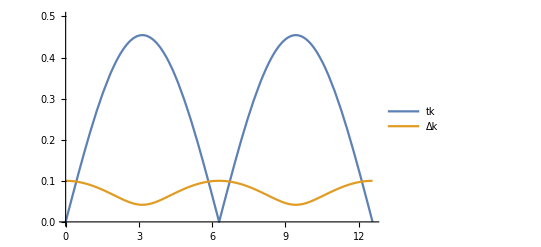

```mathematica
Block[{curves,ϕ=Function[n,x n],V=0,Δ=1,tratio=.2,tso,t=.5Δ,Vz=1.1Δ,U=0,μs},
tso=tratio*t;
μs = μsol[Vz,U,V,Δ];
Print[{ϕ[1],ϕ[2]}];
Print[Vz];
Print[μs];
Print[{μK[1],μK[2]}/.βsub/.μs];
curves={tK,ΔK-VK/2}/.βsub/.μs//FullSimplify//Abs;
Print[Differences[curves/.x->2Pi]];
Plot[curves,{x,0,4π},PlotLegends->{"tk","Δk"},PlotRange->{All,{0,t}}]
]
```

```mathematica
Module[{curves = {Abs[tK],Abs[ΔK]-VK/2}/.βsub},
Manipulate[
Block[{curves2,ϕ=Function[n,x n],tso,Δ=1,Vz=Vzv,U=Uv,V=Vv,t=tv,},
tso=tratio*t;
μs = μsol[Vz,U,V,Δ];
curves2 = curves/.μs;
curves3 = curves/.μmb[Δ,Vz,U];
GraphicsRow[{Plot[curves2,{x,0,π},PlotLegends->{"tk","Δk"},PlotRange->{All,{0,t}}],
Plot[curves3,{x,0,π},PlotLegends->{"tk","Δk"},PlotRange->{All,{0,t}},PlotLabel->"simple μ"]},ImageSize->Large]
],{{tv,.5},.1,2},{{tratio,.2},0,2},{{Vzv,1.5},1,10},{{Uv,0},0,10},{{Vv,0},0,2}]]
```

```mathematica
μsol[4,3,2,1]
```

{μ[1]→8.09059,μ[2]→-1.47471}

```mathematica
μmb[1,1,1.0]
```

{μ[1]→0.618034,μ[2]→-1.61803}

```mathematica
Manipulate[
Block[{Δ=1,F,data},
F[U_?NumberQ,V_?NumberQ]:=Join[{μ[1],μ[2]}/. μsol[Vzv,Uv,V,Δ],{μ[1],μ[2]+V}/. μmb[1,Vzv,Uv]]-U/1;
data =Table[F[Uv,V],{V,0,3,.1}]//Transpose;
ListPlot[data,PlotLegends->{"μ1","μ2","μ1mb","μ2mb"},PlotRange->{All,{-5,5}},Joined->True]
],{{Vzv,1.5},1,10},{{Uv,0},0,10}]
```

```mathematica
μmb[Δ,Vzv,Uv]
```

{μ[1]→Uv/2-√((Uv/2+Vzv)^2-Δ^2),μ[2]→Uv/2+√((Uv/2+Vzv)^2-Δ^2)}

### Extra bog

```mathematica
snegspinlessfermionoperators[a2,b2]
```

```mathematica
snegrealconstants[uaa,vaa,uab,vab,uba,vba,ubb,vbb,ϕuaa,ϕvaa,ϕuab,ϕvab,ϕuba,ϕvba,ϕubb,ϕvbb]
```

```mathematica
bogsub = {a[0,n_]:>uaa*Exp[I ϕuaa] a2[0,n]+vaa Exp[I ϕvaa]a2[1,n]+uab Exp[I ϕuab]b2[0,n]+vab Exp[I ϕvab] b2[1,n],a[1,n_]:>uaa Exp[-I ϕuaa] a2[1,n]+vaa Exp[-I ϕvaa] a2[0,n]+uab Exp[-I ϕuab] b2[1,n]+vab Exp[-I ϕvab]b2[0,n],
b[0,n_]:>uba Exp[I ϕuba]a2[0,n]+vba Exp[I ϕvba] a2[1,n]+ubb Exp[I ϕubb] b2[0,n]+ Exp[I ϕvbb]vbb b2[1,n],
b[1,n_]:>uba Exp[-I ϕuba] a2[1,n]+vba Exp[-I ϕvba] a2[0,n]+ubb Exp[-I ϕubb] b2[1,n]+vbb Exp[-I ϕvbb] b2[0,n]};
```

```mathematica
Hbog = nonintHab/.bogsub;
```

```mathematica
Hbog[[2]]//Expand//Simplify
```

$Aborted

```mathematica
decouplingeqs = Assuming[Vz>Δ,Table[Coefficient[Hbog,nc[a2[n1,m1],b2[n2,m2]]],{n1,1,2},{m1,{1,2}},{n2,{1,2}},{m2,{1,2}}]//Simplify]//Flatten
```

{2 ⅇ^(-ⅈ (ϕuba+ϕubb)) (ⅇ^(ⅈ (ϕuba+ϕvba)) ubb vba-ⅇ^(ⅈ (ϕubb+ϕvbb)) uba vbb) Vz,1/Vz ⅇ^(-ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb)) ((ⅇ^(ⅈ (ϕuba+ϕubb)) tso uaa uab+ⅇ^(ⅈ (ϕuaa+ϕubb)) t uab uba-ⅇ^(ⅈ (ϕuab+ϕuba)) t uaa ubb+ⅇ^(ⅈ (ϕuaa+ϕuab)) tso uba ubb-ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvaa+ϕvab)) tso vaa vab-ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvab+ϕvba)) t vab vba+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvaa+ϕvbb)) t vaa vbb-ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvba+ϕvbb)) tso vba vbb) Vz Cos[1/2 (ϕ[1]-ϕ[2])]-ⅈ (ⅇ^(ⅈ (ϕuaa+ϕuba+ϕubb+ϕvaa)) t uab vaa Δ+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕvaa)) tso ubb vaa Δ+ⅇ^(ⅈ (ϕuab+ϕuba+ϕubb+ϕvab)) t uaa vab Δ-ⅇ^(ⅈ (ϕuaa+ϕuab+ϕubb+ϕvab)) tso uba vab Δ-ⅇ^(ⅈ (ϕuaa+ϕuba+ϕubb+ϕvba)) tso uab vba Δ+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕvba)) t ubb vba Δ+ⅇ^(ⅈ (ϕuab+ϕuba+ϕubb+ϕvbb)) tso uaa vbb Δ+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕubb+ϕvbb)) t uba vbb Δ+ⅇ^(ⅈ (ϕuba+ϕubb)) tso uaa uab √(Vz^2-Δ^2)+ⅇ^(ⅈ (ϕuaa+ϕubb)) t uab uba √(Vz^2-Δ^2)-ⅇ^(ⅈ (ϕuab+ϕuba)) t uaa ubb √(Vz^2-Δ^2)+ⅇ^(ⅈ (ϕuaa+ϕuab)) tso uba ubb √(Vz^2-Δ^2)+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvaa+ϕvab)) tso vaa vab √(Vz^2-Δ^2)+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvab+ϕvba)) t vab vba √(Vz^2-Δ^2)-ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvaa+ϕvbb)) t vaa vbb √(Vz^2-Δ^2)+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvba+ϕvbb)) tso vba vbb √(Vz^2-Δ^2)) Sin[1/2 (ϕ[1]-ϕ[2])]),0,0,1/Vz ⅇ^(-ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb)) (-(ⅇ^(ⅈ (ϕuba+ϕubb)) tso uaa uab-ⅇ^(ⅈ (ϕuaa+ϕubb)) t uab uba+ⅇ^(ⅈ (ϕuab+ϕuba)) t uaa ubb+ⅇ^(ⅈ (ϕuaa+ϕuab)) tso uba ubb-ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvaa+ϕvab)) tso vaa vab+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvab+ϕvba)) t vab vba-ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvaa+ϕvbb)) t vaa vbb-ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvba+ϕvbb)) tso vba vbb) Vz Cos[1/2 (ϕ[1]-ϕ[2])]+ⅈ (ⅇ^(ⅈ (ϕuaa+ϕuba+ϕubb+ϕvaa)) t uab vaa Δ-ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕvaa)) tso ubb vaa Δ+ⅇ^(ⅈ (ϕuab+ϕuba+ϕubb+ϕvab)) t uaa vab Δ+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕubb+ϕvab)) tso uba vab Δ+ⅇ^(ⅈ (ϕuaa+ϕuba+ϕubb+ϕvba)) tso uab vba Δ+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕvba)) t ubb vba Δ-ⅇ^(ⅈ (ϕuab+ϕuba+ϕubb+ϕvbb)) tso uaa vbb Δ+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕubb+ϕvbb)) t uba vbb Δ+ⅇ^(ⅈ (ϕuba+ϕubb)) tso uaa uab √(Vz^2-Δ^2)-ⅇ^(ⅈ (ϕuaa+ϕubb)) t uab uba √(Vz^2-Δ^2)+ⅇ^(ⅈ (ϕuab+ϕuba)) t uaa ubb √(Vz^2-Δ^2)+ⅇ^(ⅈ (ϕuaa+ϕuab)) tso uba ubb √(Vz^2-Δ^2)+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvaa+ϕvab)) tso vaa vab √(Vz^2-Δ^2)-ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvab+ϕvba)) t vab vba √(Vz^2-Δ^2)+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvaa+ϕvbb)) t vaa vbb √(Vz^2-Δ^2)+ⅇ^(ⅈ (ϕuaa+ϕuab+ϕuba+ϕubb+ϕvba+ϕvbb)) tso vba vbb √(Vz^2-Δ^2)) Sin[1/2 (ϕ[1]-ϕ[2])]),2 ⅇ^(-ⅈ (ϕuba+ϕubb)) (ⅇ^(ⅈ (ϕuba+ϕvba)) ubb vba-ⅇ^(ⅈ (ϕubb+ϕvbb)) uba vbb) Vz,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[decouplingeqs]-Length[Select[decouplingeqs,#==0&]]
```

4

```mathematica
Solve[decouplingeqs==0]
```

$Aborted

### Naive bound

```mathematica
naivebound = μ0*tratio+V/Vz<t Δ
```

V/Vz+tratio μ0<t Δ

```mathematica
naivebound/.μ0->Sqrt[(Vz+U/2)^2-Δ^2]-U/2//Simplify
```

V/Vz+tratio (-U/2+√((U/2+Vz)^2-Δ^2))<t Δ

```mathematica
Solve[V/Vz+tratio (-U/2+√((U/2+Vz)^2-Δ^2))==t Δ,U]//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{U→(V^2-2 t V Vz Δ+Vz^2 (t^2 Δ^2+tratio^2 (-Vz^2+Δ^2)))/(tratio Vz (V+Vz (tratio Vz-t Δ)))}}

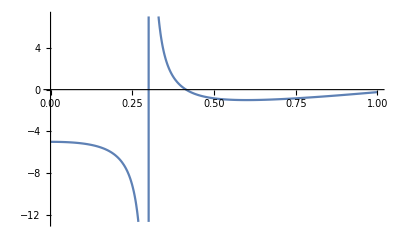

```mathematica
Block[{tratio=.2,Vz=1.5,Δ=1,t=.5},
Plot[U/.%43[[1]],{V,0,1}]]
```

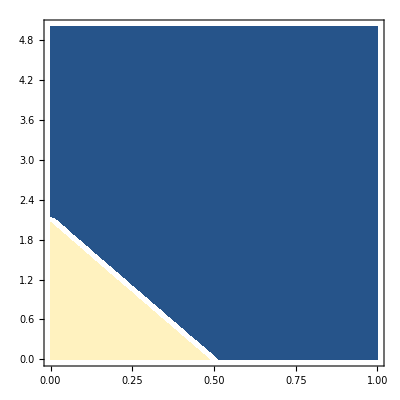

```mathematica
Module[{tratio=.2,Vz=3,Δ=1,t=.5},ContourPlot[If[V/Vz+tratio *t(+U/2+√((U/2+Vz)^2-Δ^2)+V)<t Δ,1,0],{V,0,1},{U,0,5}]]
```

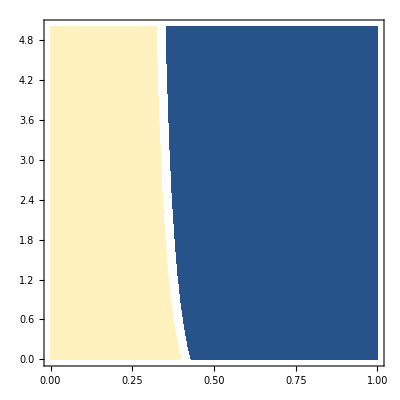

```mathematica
Module[{tratio=.4,Vz=1.5,Δ=1,t=.5},ContourPlot[If[V/Vz+tratio *t(-U/2+√((U/2+Vz)^2-Δ^2))<t Δ,1,0],{V,0,1},{U,0,5}]]
```